```mathematica
Do[a[i]=3+i, {i,2}]
Do[b[i]=4+i, {i, 5}]
Do[c[i]=7+i, {i, 3}]
```

11

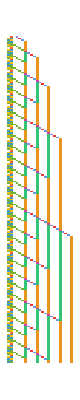

```mathematica
rules1={{0, 1, 0}->2, {0, 0, 1}->3, {0, 3, 2}->2, {3, 2, 0}->3, {0, 2, 3}->4, {2, 3, 0}->2, {0, 4, 2}->2, {4, 2, 0}->4, {0, 2, 4}->3, {2, 4, 0}->4, {0, 3, 4}->4, {3, 4, 0}->3, {3, 4, a[1]}->3, {0, 4, 3}->0, {4, 3, 0}->1, {4, 0, 0}->a[1], {a[1], 0, _}->a[1], {b[1], 0, 0}->b[2], {b[2], 0, _}->b[3], {b[3], 0, 0}->b[4], {0, b[4], 0}->c[1], {0, c[1], _}->c[1], {a[1], c[1], 0}->c[2], {0, c[2], 0}->c[3],{0, c[3], _}->c[3], {a[1], c[3], 0}->c[1], {c[2], 0, 0}->b[1], {b[3], c[1], 0}->c[2], {b[3], c[3], 0}->c[1]};

k=Max[Select[Flatten@Keys[rules1], IntegerQ]]+1
rules2=Table[IntegerDigits[i,k, 3]/.Join[rules1, {_->0}], {i, 0, k^3-1}];
rules3=FromDigits[Reverse[rules2], k];
ArrayPlot[CellularAutomaton[{rules3, k}, {{1, 0, b[1]}, 0},200], ColorRules->"Colors"]
```

```mathematica
ArrayPlot[CellularAutomaton[{rules3, k}, {{1, 0, b[1]}, 0},10000], ColorRules->"Colors", ImageSize->{Automatic, 100000}]
```

-Graphics-